```mathematica
RandomSeed
```

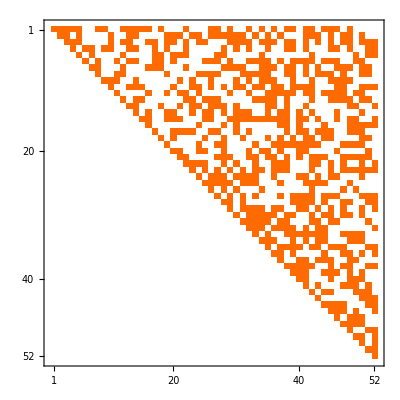

```mathematica
a=With[
{size=52},
Table[Table[If[i<j,0,If[i==j,1,RandomInteger[1]]],{i,1,size}],{j,1,size}]
];MatrixPlot[a]
```

```mathematica
Det[a]
```

1

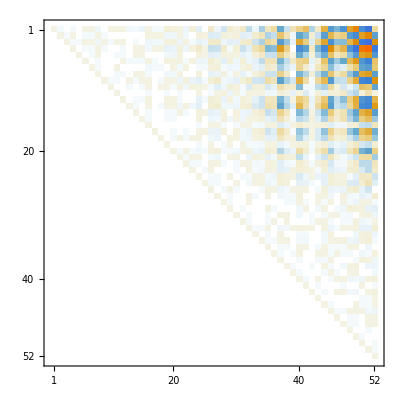

```mathematica
Inverse[a]//MatrixPlot
```

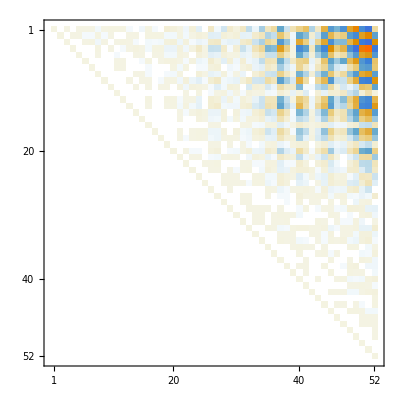

```mathematica
a+Inverse[a]//MatrixPlot
```

```mathematica
a=ConversionMatrix["E","C"];
```

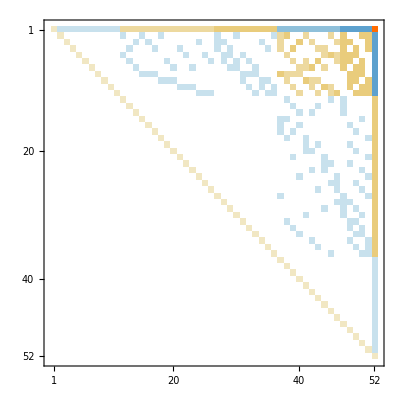
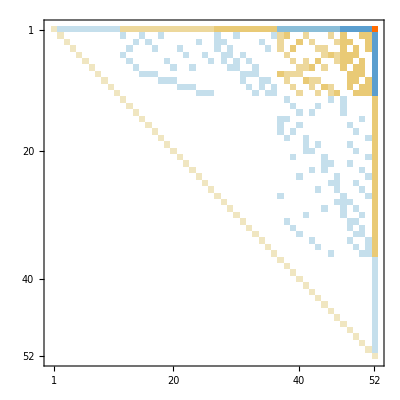
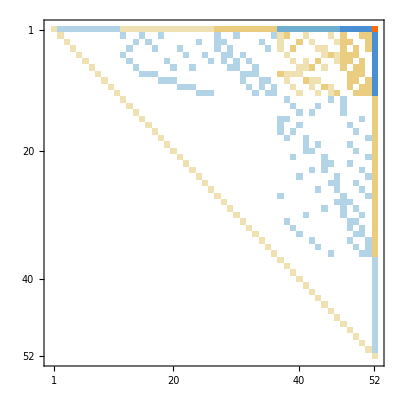
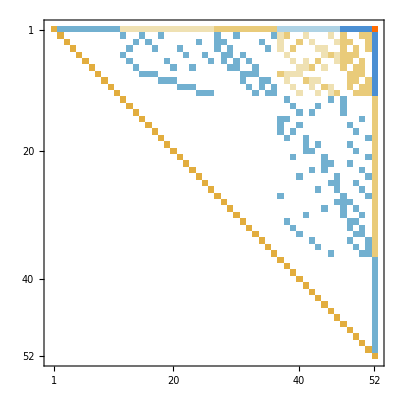
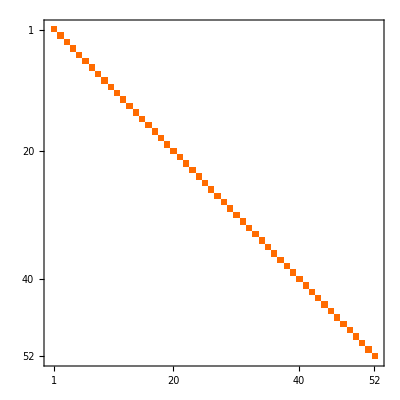
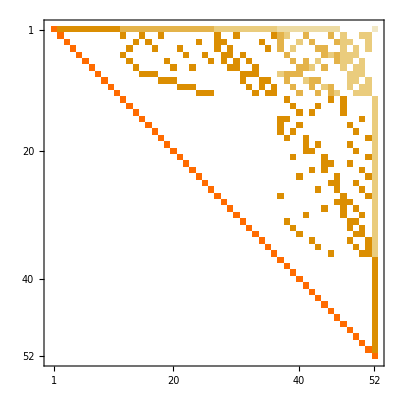
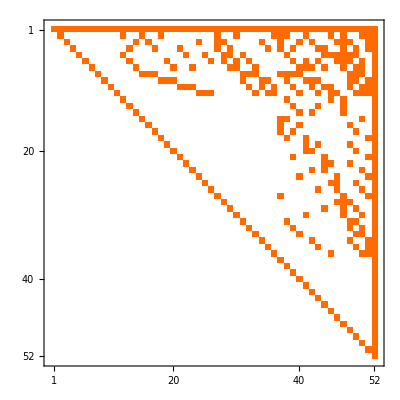
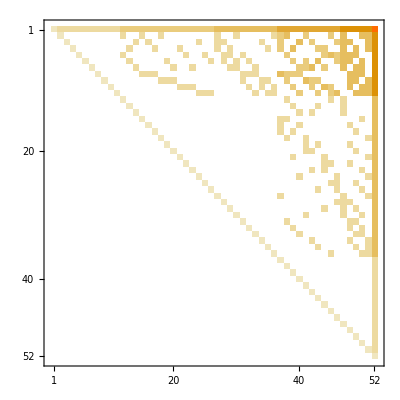
{-Graphics--2,-Graphics--3/2,-Graphics--1,-Graphics--1/2,-Graphics-0,-Graphics-1/2,-Graphics-1,-Graphics-3/2,-Graphics-2}

```mathematica
Table[Labeled[MatrixPlot[MatrixPower[a,k]],k],{k,-2,2,1/2}]
```

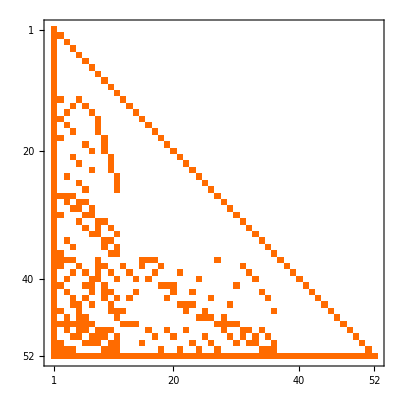

```mathematica
ConversionMatrix["E","C"]//ConjugateTranspose//MatrixPlot
```

```mathematica
Lagrange
```

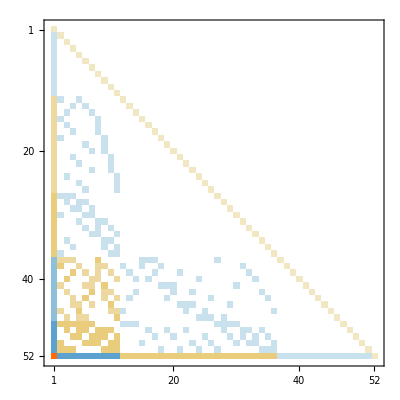
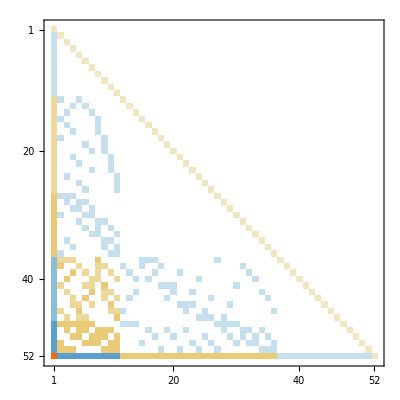
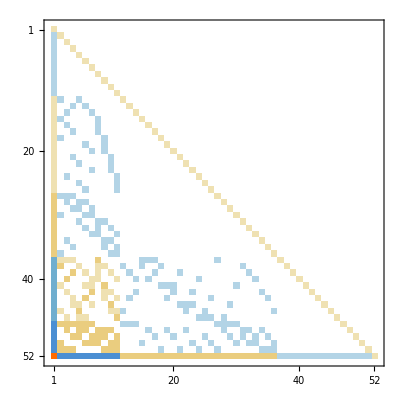
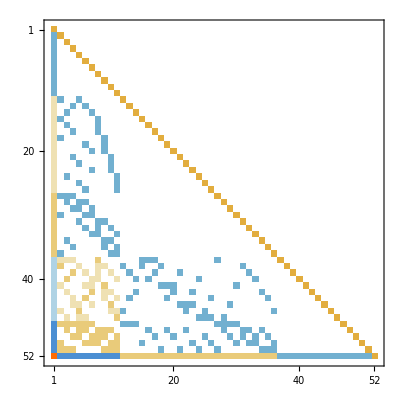
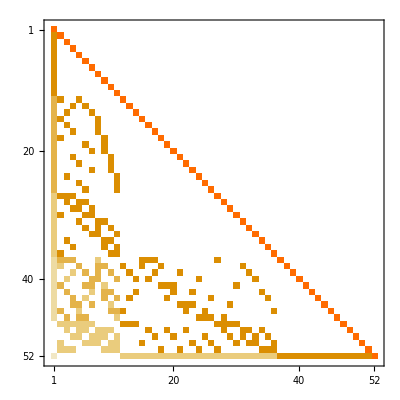
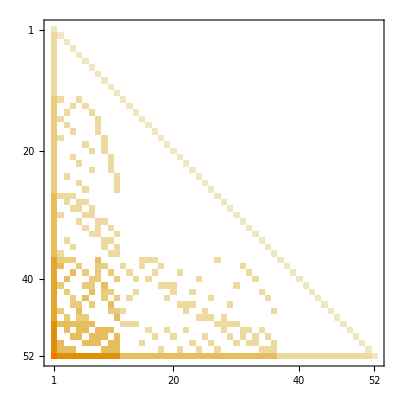
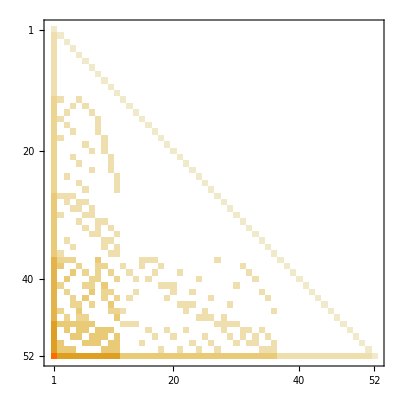
{-Graphics--2,-Graphics--3/2,-Graphics--1,-Graphics--1/2,-Graphics-0,-Graphics-1/2,-Graphics-1,-Graphics-3/2,-Graphics-2}

```mathematica
With[{mat=ConversionMatrix["F","C"]},
Table[Labeled[MatrixPlot[MatrixPower[mat,k]],k],{k,-2,2,1/2}]
];
```